## I. Build The Equivalent Triangulation Polygon

```mathematica
Parentheses2Polygon[s_, label_]:= Module[{chars = Characters[s], pos, rawtokens, tokens = {}, n,i, edges},
pos = Flatten[Position[chars, "A"]];
n = Length[pos] + 1;
tokens = ReadList[StringToStream[s], Word, TokenWords->{"(","A",")"}];
tokens = Select[tokens, # ≠ "A" &];
edges =Table[i<->(i+1), {i,n-1}];
(*AppendTo[edges, n<->1];*)
SplitParentheses[tokens_]:= Module[{index, k, t, t1, len = Length[tokens]},
t = Part[tokens, Range[2, len - 1]];
len = len - 2;
For[k = 1, k ≤ len - 1, k++,
	t1= Take[t, k];
	If[Length[Select[t1, # == "(" &]]==  Length[Select[t1, # == ")" &]], Return[{t1, Drop[t, k]}];];
];
Return[{{},{}}];
];

ProcessEdges[tokens_]:=Module[{e,v1, v2, t1, t2, t= SplitParentheses[tokens]},
	t1 = t[[1]];
	t2 = t[[2]];
	v1 =  ToExpression[First[Select[t[[1]], # ≠ "(" && #≠ ")"&]]];
	v2 =  ToExpression[Last[Select[t[[1]], # ≠ "(" && #≠ ")"&]]] + 1;	
	AppendTo[edges, v1<->v2];
	v1 =  ToExpression[First[Select[t[[2]], # ≠ "(" && #≠ ")"&]]];
	v2 =  ToExpression[Last[Select[t[[2]], # ≠ "(" && #≠ ")"&]]] + 1;	
	AppendTo[edges, v1<->v2];
	If[Length[t1] > 1, ProcessEdges[t1];];
	If[Length[t2] >1, ProcessEdges[t2];];
];
ProcessEdges[tokens];
circleLayout[n_]:=Table[{Cos[-2π/n i-π/2],Sin[-2π/n i-π/2]},{i,n}];
Graph[Range[n], DeleteDuplicates[edges], VertexLabels->Table[i ->label[[i]], {i, n}], VertexCoordinates-> circleLayout[n]]
]

Parentheses2Polygon[s_]:= Parentheses2Polygon[s, Range[Length[Flatten[Position[Characters[s], "A"]]]+1]];
```

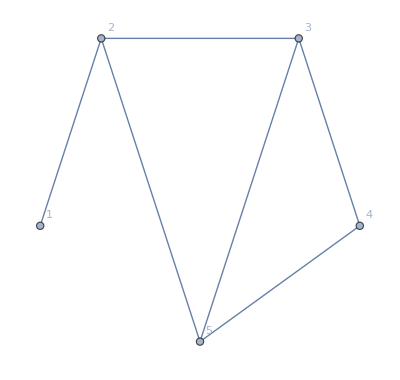

```mathematica
Parentheses2Polygon["(A1(A2(A3A4)))"]
```

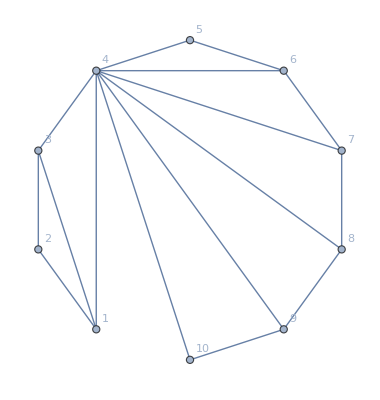

```mathematica
Parentheses2Polygon["(((A1A2)A3)(((((A4A5)A6)A7)A8)A9))"]
```

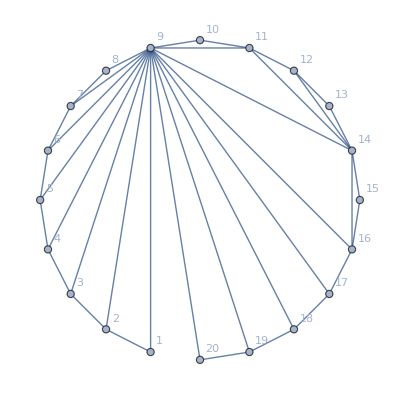

```mathematica
Parentheses2Polygon["((A1(A2(A3(A4(A5(A6(A7A8)))))))(((((((A9A10)(A11(A12A13)))(A14A15))A16)A17)A18)A19))"]
```

## I. DP for matrix chain multiplication

```mathematica
MCOPM[p_]:= Module[{MAX = 10^15, n = Length[p]-1, ans, i,j,t, np},
M = ConstantArray[MAX, {n, n}];
S = ConstantArray[{}, {n,n}];
subproblem[i_, j_]:= Module[{k,q},
If[M[[i,j]] < MAX, Return[M[[i,j]]];];
If[i == j, M[[i,j]] = 0,
For[k = i, k ≤ j-1, k++,
q = subproblem[i, k] + subproblem[k+1, j] + p[[i]]+p[[k+1]]+p[[j+1]];
If[q < M[[i,j]], M[[i,j]] = q;];
];
];
Return[M[[i,j]]];
];
ans = subproblem[1, n];
For[i = 1, i≤ n-1, i++,
For[j = i+1, j ≤ n, j++,
For[t=i, t≤ j-1, t++,
If[M[[i,j]] == M[[i, t]] + M[[t+1, j]] + p[[i]]+p[[t+1]]+p[[j+1]],AppendTo[S[[i,j]], t]];
];
];
];

f[i_, x_, y_]:=x[[i]]<>#&/@y;
g[x_,y_] := Flatten[f[#,x,y]&/@Range[Length[x]]];

getoptimal[i_, j_]:=Module[{res,res1, temp, opt, k},
res = {""};
If[i == j, Return[{"A"<> ToString[j]} ], 
	res = # <>"("& /@ res;
	opt = S[[i,j]];
         res1 = {};
	For[k = 1, k≤ Length[opt], k++,
            temp  = g[res, getoptimal[i, opt[[k]]]];
            temp = g[temp, getoptimal[opt[[k]] + 1, j]];
	   temp = #<>")" &/@ temp;
	   res1 = Join[res1, temp];
       ];
Return[res1];
];
];
(*Print[M//TableForm];
Print[S//TableForm];*)
Print[ans];
np = getoptimal[1,n];
Print[np];
Parentheses2Polygon[#, p]&/@ np//TableForm
]


HorizontalArcs[p_]:= Module[{edges={},stack={}, p1,nodes,Vmin,v,t, i, len = Length[p]},
Vmin = Position[p, Min[p]][[1,1]];
p1 = Join[Drop[p,Vmin-1], Take[p, Vmin-1]];
nodes =Range[len];
i = 1;
v = p1[[i]];
While[i ≤ len-1,
	AppendTo[stack, i];
	v = p1[[++i]];
	While[p1[[Last[stack]]] > v,
		t = Last[stack];
		stack = Delete[stack, Length[stack]];
		AppendTo[edges, Last[stack]-> t];
		AppendTo[edges, t-> i];
	];
];

circleLayout[n_]:=Table[{Cos[-2π/n i-π/2],Sin[-2π/n i-π/2]},{i,n}];
Graph[nodes,DeleteDuplicates[edges],VertexLabels->Table[i ->p1[[i]], {i, len}], VertexCoordinates-> circleLayout[len]]
];
```

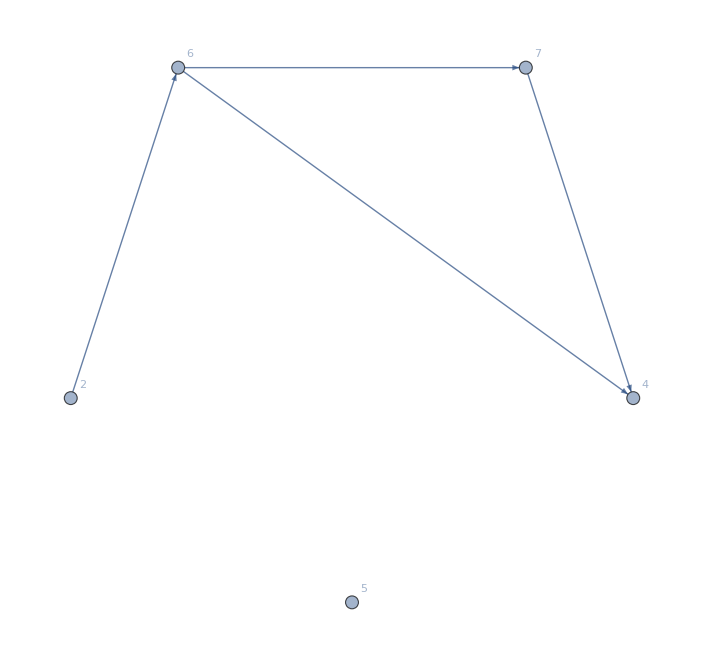

```mathematica
HorizontalArcs[{4,5,2,6,7}]
```

18

{(A1(A2(A3A4))),(A1((A2A3)A4)),((A1A2)(A3A4)),((A1(A2A3))A4),(((A1A2)A3)A4)}

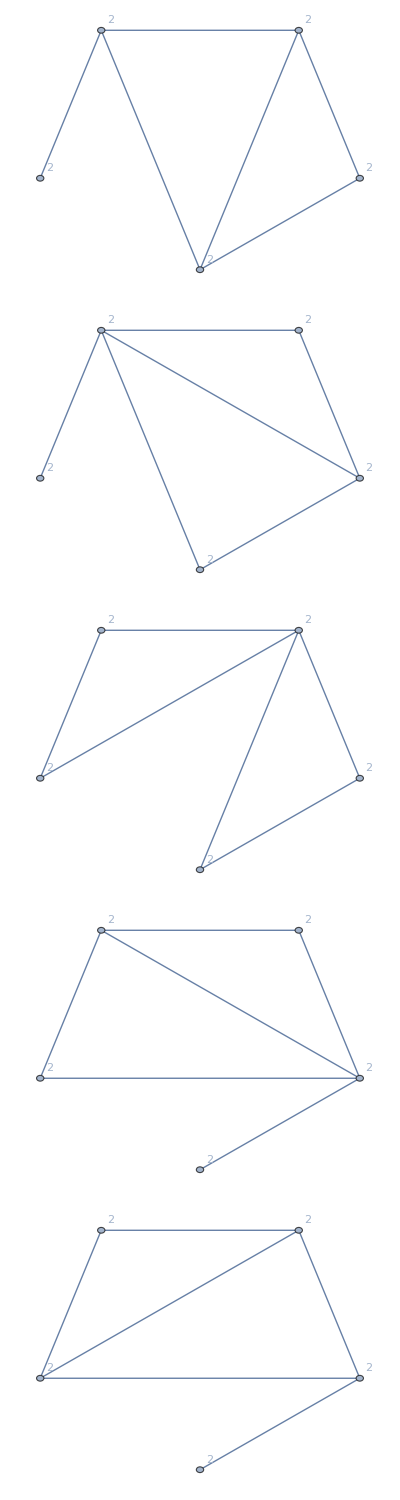

```mathematica
MCOPM[{2,2,2,2,2}]
```

```mathematica
RandomInteger[{200, 1000},50]
```

{726,391,652,680,346,319,454,732,261,446,222,456,714,504,327,375,570,719,268,380,372,952,290,305,865,786,348,665,368,778,408,540,441,328,533,672,404,919,502,929,699,880,907,456,432,566,254,346,535,307}

42893

{((((A1A2)(A3A4))((A5(A6(A7(A8(A9(A10A11))))))(((((A12A13)A14)A15)(((A16A17)A18)(((A19A20)(A21(A22A23)))((A24A25)(A26(A27A28))))))((A29A30)A31))))(((((((((((((A32(A33(((A34A35)A36)(A37A38))))(A39(A40A41)))A42)A43)A44)A45)A46)A47)A48)A49)A50)(A51A52))(A53(A54(A55A56)))))}

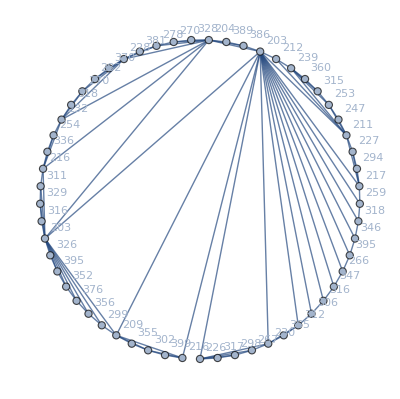

```mathematica
MCOP[{216,399,302,355,209,299,356,376,352,395,326,203,316,329,311,216,336,254,232,318,270,282,370,228,381,278,270,328,204,389,386,203,212,239,360,315,253,247,211,227,294,217,259,318,346,395,266,347,316,306,312,365,230,267,298,317,226}]
```

70288

{(A1(A2((A3(A4(A5(A6(A7(A8(A9(A10((A11(A12A13))((A14(A15A16))((((A17A18)A19)(A20A21))((A22A23)((A24A25)(A26(A27(A28(A29(A30(A31(A32((A33A34)A35)))))))))))))))))))))(((((((((A36A37)A38)A39)A40)(A41A42))A43)A44)(A45A46))((A47A48)A49)))))}

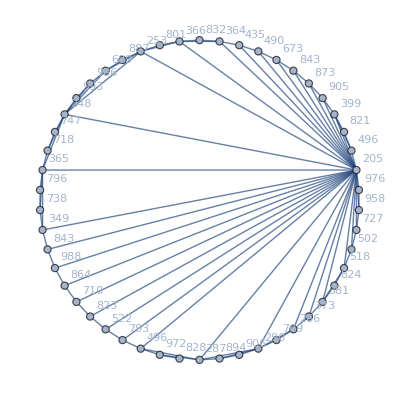

```mathematica
MCOP[{828,972,496,793,522,823,710,864,988,843,349,738,796,365,718,747,248,993,986,689,887,253,801,366,832,364,435,490,673,843,873,905,399,821,496,205,976,958,727,502,518,824,381,373,266,709,290,906,894,287}]
```

{200,205,202,203,201,200,204,200,200,201}

4822

{(((((A1A2)(A3A4))A5)((A6A7)A8))A9),((((((A1A2)A3)A4)A5)((A6A7)A8))A9),((((((A1A2)(A3A4))A5)(A6A7))A8)A9),(((((((A1A2)A3)A4)A5)(A6A7))A8)A9)}

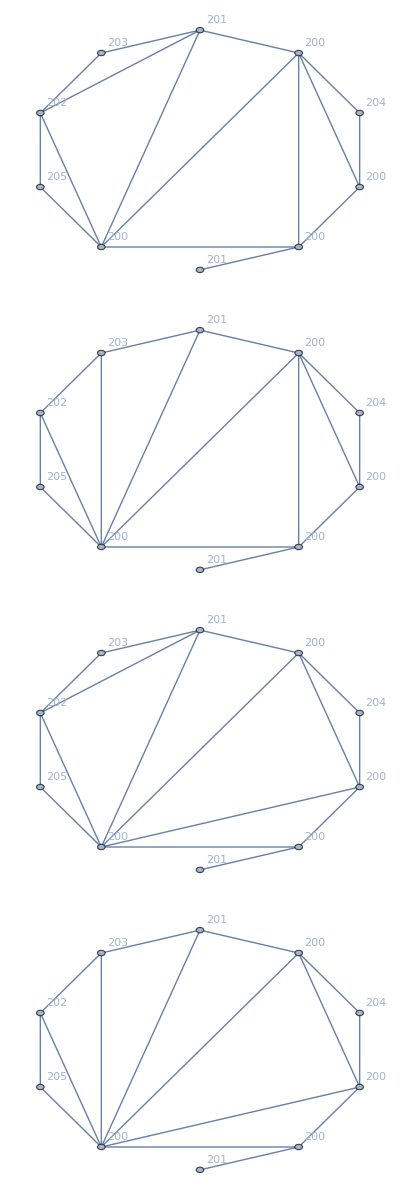

```mathematica
a = RandomInteger[{200,205}, 10]
MCOP[a]
```

{135,133,128,138,139,119,128,126,103,115}

2905

{((A1(A2(A3(A4(A5(A6(A7A8)))))))A9)}

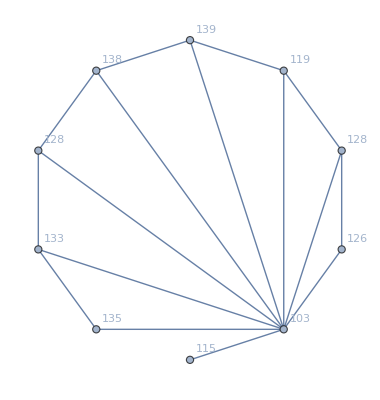

```mathematica
a = RandomInteger[{100, 150}, 10]
MCOP[a]
```

15290

{(A1(((A2((A3(A4A5))(A6A7)))(((((A8(A9(A10(A11A12))))A13)A14)A15)(A16(A17A18))))A19))}

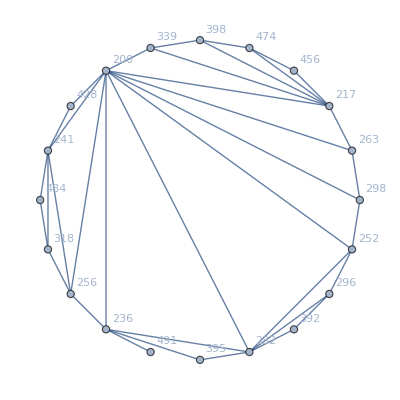

```mathematica
MCOP[RandomInteger[{200,500}, 20]]
```

17295

{((A1(A2(A3(A4((((A5A6)(A7(A8(A9A10))))A11)((A12A13)(A14(A15(A16A17)))))))))(A18A19))}

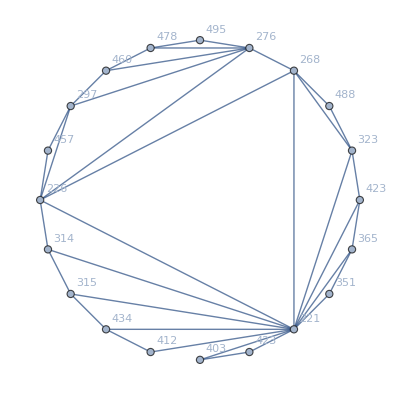

```mathematica
MCOP[RandomInteger[{200,500}, 20]]
```

1918

{((((((A1A2)A3)A4)A5)A6)A7)}

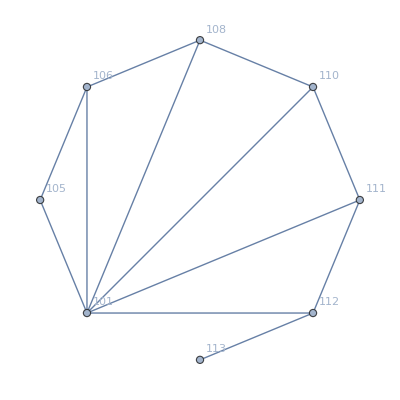

```mathematica
MCOP[{101,105,106,108,110,111,112,113}]
```

{19,18,19,20,12,10,17}

209

{((A1((A2A3)A4))(A5A6))}

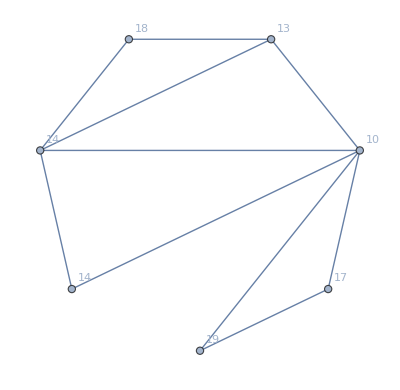

```mathematica
a = RandomInteger[{10, 20}, 7]
MCOPM[{14,14,18,13,10,17,19}]
```